```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

```mathematica
Integrate[1/((x+y)^2),{x,1,2},{y,3,4}]
```

Log[25/24]

```mathematica
%//N
```

0.040822

```mathematica
Integrate[y/((1+x^2+y^2)^(3/2)),{x,0,1},{y,0,1}]
```

```mathematica
ArcSinh[1]-ArcSinh[1/(√2)]
```

```mathematica
ArcSinh[1]-ArcSinh[1/(√2)]//N
```

0.222895

```mathematica
?TrigToExp
```

TrigToExp[expr] converts trigonometric functions in expr to exponentials.

```mathematica
TrigToExp[ArcSinh[1]-ArcSinh[1/(√2)]]
```

-Log[√(3/2)+1/(√2)]+Log[1+√2]

```mathematica
%//FullSimplify
```

ArcSinh[1]+1/2 Log[2-√3]

```mathematica
r=Integrate[y/((1+x^2+y^2)^(3/2)),{x,0,1}]
```

ConditionalExpression[y/((1+y^2) √(2+y^2)),((Re[√(-1-y^2)]≤0&&((y∈Reals&&y≠0)||(Re[y]==0&&Re[y^2]≥-1&&-1<Im[y]<1)))||√(-1-y^2)∉Reals||Re[√(-1-y^2)]≥1)&&√(-1-y^2)≠0]

```mathematica
r=Assuming[Element[x,Reals],Simplify[r]];
Together[r]
```

ConditionalExpression[y/((1+y^2) √(2+y^2)),((Re[√(-1-y^2)]≤0&&((y∈Reals&&y≠0)||(Re[y]==0&&Re[y^2]≥-1&&-1<Im[y]<1)))||√(-1-y^2)∉Reals||Re[√(-1-y^2)]≥1)&&√(-1-y^2)≠0]

```mathematica
r=Integrate[y/((1+x^2+y^2)^(3/2)),{y,0,1}]
r=Assuming[Element[x,Reals],FullSimplify[r]];
Together[r]
```

ConditionalExpression[1/(√(1+x^2))-1/(√(2+x^2)),((Re[√(-1-x^2)]≤0&&((x∈Reals&&x≠0)||(Re[x]==0&&Re[x^2]≥-1&&-1<Im[x]<1)))||√(-1-x^2)∉Reals||Re[√(-1-x^2)]≥1)&&√(-1-x^2)≠0]

(-√(1+x^2)+√(2+x^2))/(√(1+x^2) √(2+x^2))

```mathematica
FullSimplify[(-√(1+x^2)+√(2+x^2))/(√(1+x^2) √(2+x^2))]
```

1/(√(1+x^2))-1/(√(2+x^2))

```mathematica
Integrate[y/((1+x^2+y^2)^(3/2)),{y,0,1}]
```

ConditionalExpression[1/(√(1+x^2))-1/(√(2+x^2)),((Re[√(-1-x^2)]≤0&&((x∈Reals&&x≠0)||(Re[x]==0&&Re[x^2]≥-1&&-1<Im[x]<1)))||√(-1-x^2)∉Reals||Re[√(-1-x^2)]≥1)&&√(-1-x^2)≠0]

```mathematica
?Assuming
```

Assuming[assum,expr] evaluates expr with assum appended to $Assumptions, so that assum is included in the default assumptions used by functions such as Refine, Simplify and Integrate.

```mathematica
Assuming[Element[x,Reals],Integrate[y/((1+x^2+y^2)^(3/2)),{y,0,1}]]
```

(-√(1+x^2)+√(2+x^2))/(√(2+3 x^2+x^4))

```mathematica
%//Simplify
```

(-√(1+x^2)+√(2+x^2))/(√(2+3 x^2+x^4))

```mathematica
?Together
```

Together[expr] puts terms in a sum over a common denominator, and cancels factors in the result.

```mathematica
Integrate[Log[(2+y)^2]-Log[(1+y)^2],{y,3,4}]
```

2 Log[11943936/9765625]

```mathematica
%//N
```

0.40271

```mathematica
?Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

```mathematica
ArcSinh[1]
```

```mathematica
ArcSinh[1]//N
```

0.881374

```mathematica
D[1/(Sqrt[1+x^2+y^2]),y]
```

-y/((1+x^2+y^2)^(3/2))

```mathematica
Integrate[y/Sqrt[1+x^2+y^2],x]
```

y Log[x+√(1+x^2+y^2)]

```mathematica
?Apart
```

Apart[expr] rewrites a rational expression as a sum of terms with minimal denominators. 
Apart[expr,var] treats all variables other than var as constants.

```mathematica
Apart[y/((1+x^2+y^2)^(3/2))]
```

y/((1+x^2+y^2)^(3/2))

```mathematica
ApartSquareFree[1/(1+x^2+y^2)]
```

```mathematica
1/(1+x^2+y^2)//FullSimplify
```

1/(1+x^2+y^2)

```mathematica
1/Sqrt[x^2+1]-1/Sqrt[x^2+2]//Simplify
```

1/(√(1+x^2))-1/(√(2+x^2))

```mathematica
%//FullSimplify
```

1/(√(1+x^2))-1/(√(2+x^2))

```mathematica
Integrate[1/Sqrt[x],x]
```

2 √x

```mathematica
Integrate[2 y*Sqrt[(2+y^2)^3]-2 y*Sqrt[(1+y^2)^3],{y,0,1}]
```

-2/5 (-1+8 √2-9 √3)

```mathematica
%//N
```

2.1099

```mathematica
f[x_,k_]:=-1/(x^(1+1/k))
```

```mathematica
?Limit
```

Limit[expr,x->x_0] finds the limiting value of expr when x approaches x_0.

```mathematica
Limit[f[x,k],k->∞]
```

-1/x

```mathematica
Integrate[-1/(x^(1+1/k)),x]
```

k x^(-1/k)

```mathematica
Limit[k x^(-1/k),k->∞]
```

∞

```mathematica
1/√(x^2+1)-1/√(x^2+2)//FullSimplify
```

1/(√(1+x^2))-1/(√(2+x^2))

```mathematica
(x^2+2)(x^2+1)//Expand
```

2+3 x^2+x^4

```mathematica
(1+x^2+y^2)^(3/2)//Expand
```

√(1+x^2+y^2)+x^2 √(1+x^2+y^2)+y^2 √(1+x^2+y^2)

```mathematica
%//FullSimplify
```

(1+x^2+y^2)^(3/2)

```mathematica
Integrate[y/((1+x^2+y^2)^(3/2)),x]
```

(x y)/((1+y^2) √(1+x^2+y^2))

```mathematica
Integrate[(x y)/((1+y^2) √(1+x^2+y^2)),y]
```

-ArcTanh[(√(1+x^2+y^2))/x]

```mathematica
Integrate[1/z^(3/2),z]
```

-2/(√z)

```mathematica
D[1/√(y^2+1)-1/√(y.b2+2),y]
```

```mathematica
-y/((1+y^2)^(3/2))//FullSimplify
```

-y/((1+y^2)^(3/2))

```mathematica
FullSimplify[-y/((1+y^2)^(3/2))*2y]
```

-(2 y^2)/((1+y^2)^(3/2))

```mathematica
Integrate[2y/((1+x^2+y^2)^(3/2)),{x,0,1}]
```

ConditionalExpression[(2 y)/((1+y^2) √(2+y^2)),((Re[√(-1-y^2)]≤0&&((y∈Reals&&y≠0)||(Re[y]==0&&Re[y^2]≥-1&&-1<Im[y]<1)))||√(-1-y^2)∉Reals||Re[√(-1-y^2)]≥1)&&√(-1-y^2)≠0]

```mathematica
Integrate[2 y(1/√(y^2+1)-1/√(y^2+2)),{y,0,1}]
```

-2+4 √2-2 √3

```mathematica
-2+4 √2-2 √3//N
```

0.192753

```mathematica
((x y)/((1+y^2) √(1+x^2+y^2)))==2 y(1/√(y^2+1)-1/√(y^2+2))
```

(x y)/((1+y^2) √(1+x^2+y^2))==2 y (1/(√(1+y^2))-1/(√(2+y^2)))

```mathematica
Integrate[y/Sqrt[2+y^2],{y,0,1}]
```

-√2+√3

```mathematica
-2+2 Sqrt[3]
```

-2+2 √3

```mathematica
%//N
```

1.4641

```mathematica
Integrate[1/(Sqrt[1+x^2+y^2])^3,{x,0,1}]
```

ConditionalExpression[1/((1+y^2) √(2+y^2)),((Re[√(-1-y^2)]≤0&&((y∈Reals&&y≠0)||(Re[y]==0&&Re[y^2]≥-1&&-1<Im[y]<1)))||√(-1-y^2)∉Reals||Re[√(-1-y^2)]≥1)&&√(-1-y^2)≠0]

```mathematica
Log[(1+Sqrt[2])/(1+Sqrt[3])]-Log[1/Sqrt[2]]
```

Log[2]/2+Log[(1+√2)/(1+√3)]

```mathematica
%//N
```

0.222895

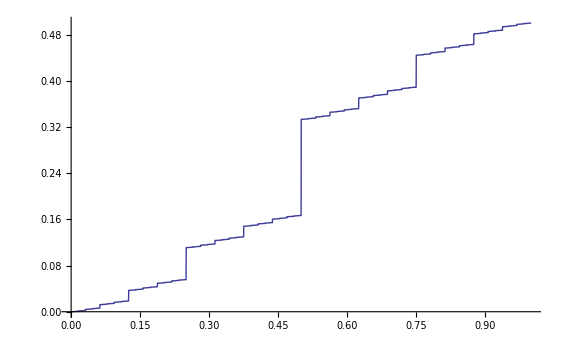

```mathematica
Plot[FromDigits[RealDigits[x,2,9],3],{x,0,1}]
```

```mathematica
?FromDigits
```

FromDigits[list] constructs an integer from the list of its decimal digits. 
FromDigits[list,b] takes the digits to be given in base b. 
FromDigits[string] constructs an integer from a string of digits.
FromDigits[string,Roman] constructs an integer from Roman numerals.